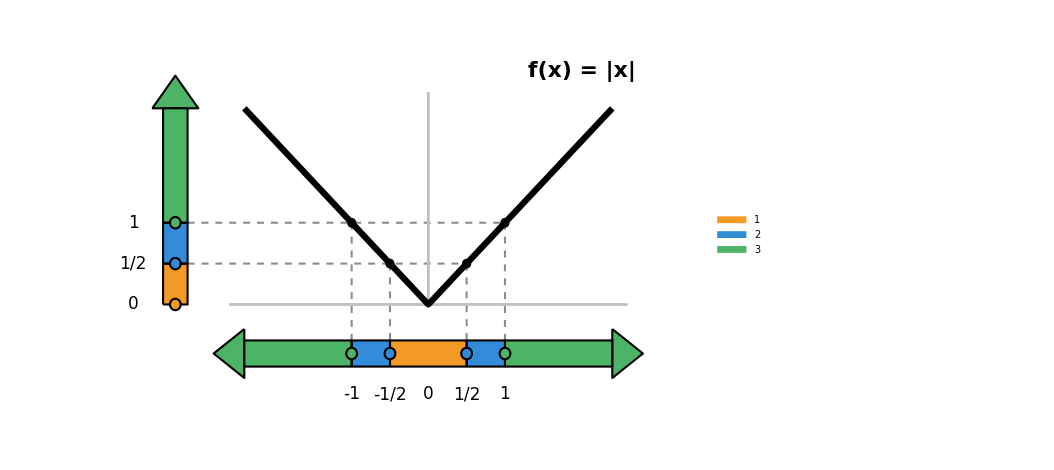

```mathematica
ClearAll[colE0, colE1, colF1, rr, xV, yH, cerrado, bandaV, bandaH, rangoBandas, dominioBandas,
  guias, grafica, etiquetas, grafico1, diagrama1];

colE0 = RGBColor[0.95, 0.6, 0.15];    (* E_{1,0}: f toma valores en [0,1/2) *)
colE1 = RGBColor[0.2, 0.55, 0.85];    (* E_{1,1}: f toma valores en [1/2,1) *)
colF1 = RGBColor[0.3, 0.7, 0.4];      (* F_1: f toma valores en [1,∞] *)
rr = 0.07;
xV = -3.3;    (* barra vertical: espacio de llegada *)
yH = -0.6;    (* barra horizontal: espacio de partida *)

cerrado[p_, col_] := {col, EdgeForm[{Black, AbsoluteThickness[1.5]}], Disk[p, rr]};
bandaV[y1_, y2_, col_] := {col, EdgeForm[{Black, AbsoluteThickness[1.5]}],
   Rectangle[{xV - 0.16, y1}, {xV + 0.16, y2}]};
bandaH[x1_, x2_, col_] := {col, EdgeForm[{Black, AbsoluteThickness[1.5]}],
   Rectangle[{x1, yH - 0.16}, {x2, yH + 0.16}]};

(* el rango [0,∞] partido en [0,1/2), [1/2,1) y [1,∞]; cada corte pertenece a la banda de arriba *)
rangoBandas = {
   bandaV[0, 0.5, colE0], bandaV[0.5, 1, colE1], bandaV[1, 2.4, colF1],
   {colF1, EdgeForm[{Black, AbsoluteThickness[1.5]}],
    Polygon[{{xV - 0.3, 2.4}, {xV + 0.3, 2.4}, {xV, 2.8}}]},
   cerrado[{xV, 0}, colE0], cerrado[{xV, 0.5}, colE1], cerrado[{xV, 1}, colF1]};

(* las antiimágenes en el dominio: E_{1,0}, E_{1,1} (dos trozos) y F_1 (dos semirrectas) *)
dominioBandas = {
   bandaH[-0.5, 0.5, colE0], bandaH[-1, -0.5, colE1], bandaH[0.5, 1, colE1],
   bandaH[-2.4, -1, colF1], bandaH[1, 2.4, colF1],
   {colF1, EdgeForm[{Black, AbsoluteThickness[1.5]}],
    Polygon[{{-2.4, yH + 0.3}, {-2.4, yH - 0.3}, {-2.8, yH}}],
    Polygon[{{2.4, yH + 0.3}, {2.4, yH - 0.3}, {2.8, yH}}]},
   cerrado[{-1, yH}, colF1], cerrado[{1, yH}, colF1],
   cerrado[{-0.5, yH}, colE1], cerrado[{0.5, yH}, colE1]};

(* desde cada corte del rango, horizontal hasta la gráfica y vertical hasta el dominio *)
guias = {GrayLevel[0.55], Dashed, AbsoluteThickness[1.5],
   Line[{{xV + 0.16, 0.5}, {0.5, 0.5}}], Line[{{xV + 0.16, 1}, {1, 1}}],
   Table[Line[{{s 0.5, 0.5}, {s 0.5, yH + 0.16}}], {s, {-1, 1}}],
   Table[Line[{{s, 1}, {s, yH + 0.16}}], {s, {-1, 1}}]};

grafica = {GrayLevel[0.75], AbsoluteThickness[2],
   Line[{{-2.6, 0}, {2.6, 0}}], Line[{{0, 0}, {0, 2.6}}],
   Black, AbsoluteThickness[4.5], Line[{{-2.4, 2.4}, {0, 0}, {2.4, 2.4}}],
   Table[{Black, Disk[{s, Abs[s]}, 0.06]}, {s, {-1, -0.5, 0.5, 1}}]};

etiquetas = {Black,
   Table[Text[Style[p[[2]], 17], {xV - 0.55, p[[1]]}], {p, {{0, "0"}, {0.5, "1/2"}, {1, "1"}}}],
   Table[Text[Style[p[[2]], 17], {p[[1]], yH - 0.5}],
    {p, {{-1, "-1"}, {-0.5, "-1/2"}, {0, "0"}, {0.5, "1/2"}, {1, "1"}}}],
   Text[Style["f(x) = |x|", 22, Bold], {2.0, 2.85}]};

grafico1 = Graphics[{guias, grafica, rangoBandas, dominioBandas, etiquetas},
   PlotRange -> {{-4.4, 3.4}, {-1.5, 3.2}}, ImageSize -> 780];

diagrama1 = Legended[grafico1,
   SwatchLegend[{colE0, colE1, colF1}, {Subscript["E", "1,0"], Subscript["E", "1,1"], Subscript["F", 1]},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama1

Export[CloudObject["T3_P57_particion"], diagrama1,"PNG", Background -> None,ImageResolution -> 300];
```

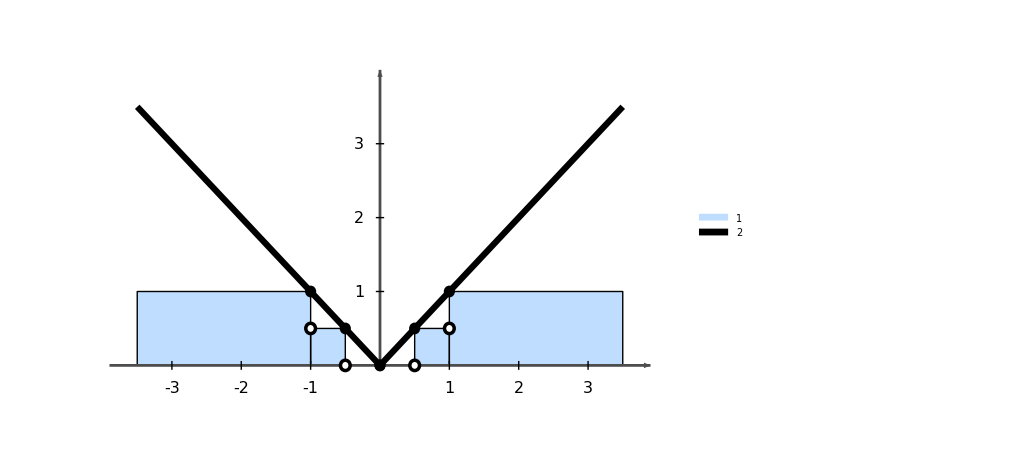

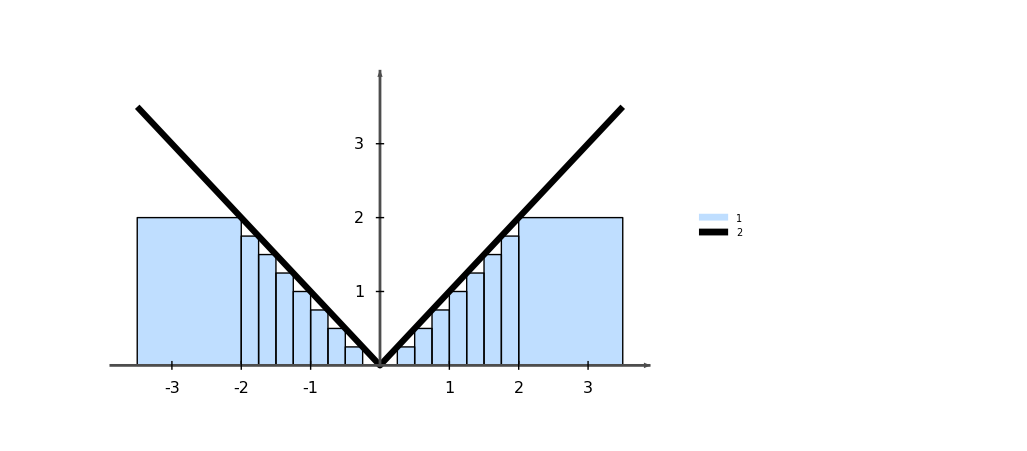

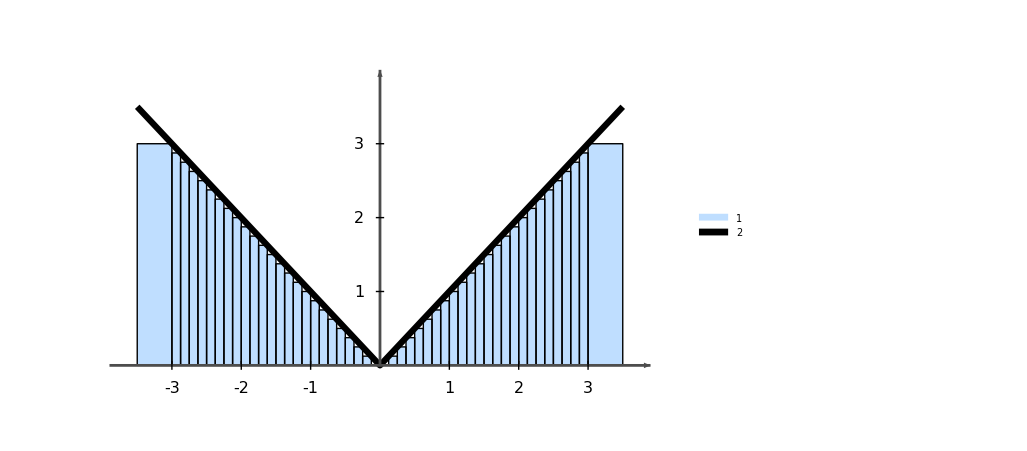

```mathematica
ClearAll[L, colBar, rr, cerrado, abierto, escalera, diagrama2, diagrama3, diagrama4];

L = 3.5;
colBar = RGBColor[0.75, 0.87, 1];
rr = 0.07;

cerrado[p_, col_] := {col, Disk[p, rr]};
abierto[p_, col_] := {White, Disk[p, rr], col, AbsoluteThickness[2.5], Circle[p, rr]};

(* peldaño k: valor k/2^n sobre [k/2^n,(k+1)/2^n);  a partir de |x| = n, el valor n *)
escalera[n_, puntos_] := Module[{w = 2.^-n, m = n 2^n, barras, truncado, grafica, ejes, ticks, dots},
   barras = Table[{Rectangle[{k w, 0}, {(k + 1) w, k w}],
      Rectangle[{-(k + 1) w, 0}, {-k w, k w}]}, {k, 1, m - 1}];
   truncado = {Rectangle[{n, 0}, {L, n}], Rectangle[{-L, 0}, {-n, n}]};
   grafica = {Black, AbsoluteThickness[4.5], Line[{{-L, L}, {0, 0}, {L, L}}]};
   ejes = {GrayLevel[0.3], AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{{-L - 0.4, 0}, {L + 0.4, 0}}], Arrow[{{0, 0}, {0, L + 0.5}}]};
   ticks = {Black,
     Table[{Line[{{x, -0.06}, {x, 0.06}}], Text[Style[x, 16], {x, -0.3}]},
      {x, Complement[Range[-3, 3], {0}]}],
     Table[{Line[{{-0.06, y}, {0.06, y}}], Text[Style[y, 16], {-0.3, y}]}, {y, 1, 3}]};
   (* extremos de cada peldaño: macizo a la izquierda (sobre la gráfica), hueco a la derecha *)
   dots = If[puntos,
     {Table[{cerrado[{s k w, k w}, Black], abierto[{s (k + 1) w, k w}, Black]},
       {s, {1, -1}}, {k, 0, m - 1}],
      Table[cerrado[{s n, n}, Black], {s, {1, -1}}]}, {}];
   Legended[
    Graphics[{colBar, EdgeForm[{Black, AbsoluteThickness[1]}], barras, truncado,
      grafica, ejes, ticks, dots},
     PlotRange -> {{-L - 0.7, L + 0.7}, {-0.6, L + 0.9}}, ImageSize -> 760],
    SwatchLegend[{colBar, Black}, {Subscript["f", n], "f(x) = |x|"},
     LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]]
   ];

diagrama2 = escalera[1, True];
diagrama3 = escalera[2, False];
diagrama4 = escalera[3, False];

diagrama2

diagrama3

diagrama4

Export[CloudObject["T3_P57_f1"], diagrama2,"PNG", Background -> None, ImageResolution ->300];
Export[CloudObject["T3_P57_f2"], diagrama3,"PNG", Background -> None, ImageResolution -> 300];
Export[CloudObject["T3_P57_f3"], diagrama4,"PNG", Background -> None, ImageResolution -> 300];
```

```mathematica
ClearAll[L, colN, contorno, grafico5, diagrama5];

L = 3.5;
colN = {RGBColor[0.45, 0.7, 0.95], RGBColor[0.2, 0.45, 0.85], RGBColor[0.02, 0.15, 0.55]};

(* contorno de la escalera f_n sobre x >= 0: cada peldaño sube hasta tocar |x| y se abre a la derecha *)
contorno[n_] := Module[{w = 2.^-n, m = n 2^n},
   Join[Flatten[Table[{{k w, k w}, {(k + 1) w, k w}}, {k, 0, m - 1}], 1], {{n, n}, {L, n}}]];

grafico5 = Graphics[{
    {GrayLevel[0.3], AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{{0, 0}, {L + 0.4, 0}}], Arrow[{{0, 0}, {0, L + 0.5}}]},
    {Black, AbsoluteThickness[4.5], Line[{{0, 0}, {L, L}}]},
    Table[{colN[[n]], AbsoluteThickness[3.5], Line[contorno[n]]}, {n, 1, 3}],
    {Black,
     Table[{Line[{{x, -0.06}, {x, 0.06}}], Text[Style[x, 16], {x, -0.3}]}, {x, 1, 3}],
     Table[{Line[{{-0.06, y}, {0.06, y}}], Text[Style[y, 16], {-0.3, y}]}, {y, 1, 3}]}},
   PlotRange -> {{-0.7, L + 0.7}, {-0.6, L + 0.9}}, ImageSize -> 620];

diagrama5 = Legended[grafico5,
   SwatchLegend[Append[colN, Black],
    {Subscript["f", 1], Subscript["f", 2], Subscript["f", 3], "f(x) = |x|"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama5

Export[CloudObject["T3_P57_monotonia"], diagrama5,"PNG", Background -> None,  ImageResolution -> 300];
```

-Graphics-

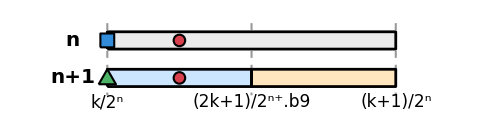
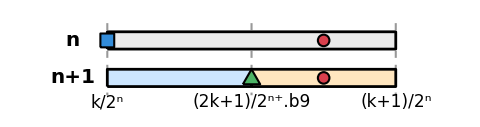
Primera mitad: no cambia
-Graphics-Segunda mitad: aumenta
-Graphics-

```mathematica
ClearAll[colF, colFn, colFn1, yA, yB, hB, barra, marcaF, marcaFn, marcaFn1, panel, panel1, panel2,
  diagrama6];

colF = RGBColor[0.85, 0.25, 0.3];      (* f(ω), disco *)
colFn = RGBColor[0.2, 0.55, 0.85];     (* f_n(ω), cuadrado *)
colFn1 = RGBColor[0.3, 0.7, 0.4];      (* f_{n+1}(ω), triángulo *)

yA = 2; yB = 0.7;   (* fila del nivel n y fila del nivel n+1 *)
hB = 0.3;           (* semialtura de las barras *)

barra[x1_, x2_, y_, col_] := {col, EdgeForm[{Black, AbsoluteThickness[2]}],
   Rectangle[{x1, y - hB}, {x2, y + hB}]};
marcaF[p_] := {colF, EdgeForm[{Black, AbsoluteThickness[1.5]}], Disk[p, 0.2]};
marcaFn[p_] := {colFn, EdgeForm[{Black, AbsoluteThickness[1.5]}],
   Rectangle[p - {0.24, 0.24}, p + {0.24, 0.24}]};
marcaFn1[p_] := {colFn1, EdgeForm[{Black, AbsoluteThickness[1.5]}],
   Polygon[{p + {-0.3, -0.22}, p + {0.3, -0.22}, p + {0, 0.3}}]};

(* pF: dónde cae f(ω);  xFn1: extremo izquierdo de la mitad que contiene a f(ω) *)
panel[pF_, xFn1_, titulo_] := Column[{
    Style[titulo, 20, Bold],
    Graphics[{
      {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
       Line[{{0, yA + hB + 0.3}, {0, yB - hB - 0.3}}],
       Line[{{5, yA + hB + 0.3}, {5, yB - hB - 0.3}}],
       Line[{{10, yA + hB + 0.3}, {10, yB - hB - 0.3}}]},
      barra[0, 10, yA, GrayLevel[0.92]],
      barra[0, 5, yB, RGBColor[0.8, 0.9, 1]], barra[5, 10, yB, RGBColor[1, 0.9, 0.75]],
      marcaF[{pF, yA}], marcaF[{pF, yB}],
      marcaFn[{0, yA}], marcaFn1[{xFn1, yB}],
      {Black,
       Text[Style["n", 20, Bold], {-1.2, yA}],
       Text[Style["n+1", 20, Bold], {-1.2, yB}],
       Text[Style["k/2ⁿ", 17], {0, yB - 0.85}],
       Text[Style["(2k+1)/2ⁿ⁺.b9", 17], {5, yB - 0.85}],
       Text[Style["(k+1)/2ⁿ", 17], {10, yB - 0.85}]}},
     PlotRange -> {{-2.2, 11.4}, {-0.6, 3.0}}, ImageSize -> 480]},
   Alignment -> Center, Spacings -> 0.5];

panel1 = panel[2.5, 0, "Primera mitad: no cambia"];
panel2 = panel[7.5, 5, "Segunda mitad: aumenta"];

diagrama6 = Legended[Row[{panel1, Spacer[40], panel2}],
   SwatchLegend[{colF, colFn, colFn1},
    {"f(ω)", Row[{Subscript["f", "n"], "(ω)"}], Row[{Subscript["f", "n+1"], "(ω)"}]},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama6

Export[CloudObject["T3_P57_subdivision"], diagrama6,"PNG", Background -> None,ImageResolution -> 300];
```

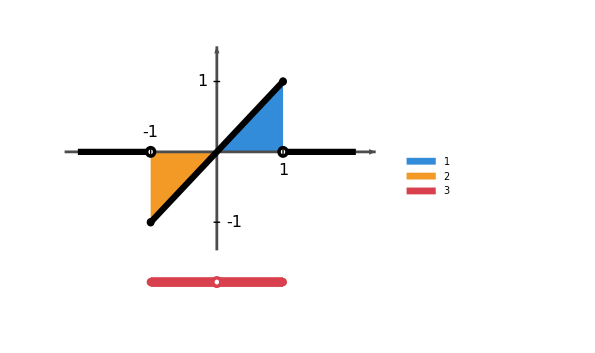
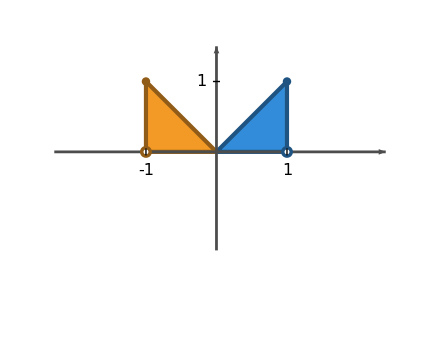
f
-Graphics-f^+  y  f^-
-Graphics-

```mathematica
ClearAll[colPos, colNeg, colPosD, colNegD, colSet, rr, cerrado, abierto, ejes, panelF, panelPN,
  tituloF, tituloPN, diagrama7];

colPos = RGBColor[0.2, 0.55, 0.85];    (* parte positiva *)
colNeg = RGBColor[0.95, 0.6, 0.15];    (* parte negativa *)
colPosD = Darker[colPos, 0.4];
colNegD = Darker[colNeg, 0.4];
colSet = RGBColor[0.85, 0.25, 0.3];    (* el conjunto {f ≠ 0} *)
rr = 0.06;

cerrado[p_, col_] := {col, Disk[p, rr]};
abierto[p_, col_] := {White, Disk[p, rr], col, AbsoluteThickness[2.5], Circle[p, rr]};

ejes = {GrayLevel[0.3], AbsoluteThickness[2], Arrowheads[0.02],
   Arrow[{{-2.3, 0}, {2.4, 0}}], Arrow[{{0, -1.4}, {0, 1.5}}]};

(* izquierda: f con signo.  Las dos áreas son iguales y se cancelan *)
panelF = Graphics[{
    {colPos, Polygon[{{0, 0}, {1, 0}, {1, 1}}]},
    {colNeg, Polygon[{{-1, 0}, {-1, -1}, {0, 0}}]},
    ejes,
    {Black, AbsoluteThickness[4.5],
     Line[{{-2.1, 0}, {-1, 0}}], Line[{{-1, -1}, {1, 1}}], Line[{{1, 0}, {2.1, 0}}]},
    abierto[{-1, 0}, Black], cerrado[{-1, -1}, Black],
    cerrado[{1, 1}, Black], abierto[{1, 0}, Black],
    {Black,
     Line[{{-0.05, 1}, {0.05, 1}}], Line[{{-0.05, -1}, {0.05, -1}}],
     Text[Style["1", 16], {-0.22, 1}], Text[Style["-1", 16], {0.26, -1}],
     Line[{{-1, -0.05}, {-1, 0.05}}], Line[{{1, -0.05}, {1, 0.05}}],
     Text[Style["-1", 16], {-1, 0.27}], Text[Style["1", 16], {1, -0.27}]},
    (* el conjunto {f ≠ 0} = [-1,1] \ {0}, con el hueco en 0 *)
    {colSet, AbsoluteThickness[7], CapForm["Butt"], Line[{{-1, -1.85}, {1, -1.85}}]},
    cerrado[{-1, -1.85}, colSet], cerrado[{1, -1.85}, colSet], abierto[{0, -1.85}, colSet]},
   PlotRange -> {{-2.5, 2.6}, {-2.4, 1.7}}, ImageSize -> 440];

(* derecha: f⁺ y f⁻, las dos por encima del eje.  Sus áreas coinciden *)
panelPN = Graphics[{
    {colPos, EdgeForm[{colPosD, AbsoluteThickness[3]}], Polygon[{{0, 0}, {1, 0}, {1, 1}}]},
    {colNeg, EdgeForm[{colNegD, AbsoluteThickness[3]}], Polygon[{{-1, 0}, {-1, 1}, {0, 0}}]},
    ejes,
    abierto[{-1, 0}, colNegD], cerrado[{-1, 1}, colNegD],
    cerrado[{1, 1}, colPosD], abierto[{1, 0}, colPosD],
    {Black,
     Line[{{-0.05, 1}, {0.05, 1}}], Text[Style["1", 16], {-0.22, 1}],
     Line[{{-1, -0.05}, {-1, 0.05}}], Line[{{1, -0.05}, {1, 0.05}}],
     Text[Style["-1", 16], {-1, -0.27}], Text[Style["1", 16], {1, -0.27}]}},
   PlotRange -> {{-2.5, 2.6}, {-2.4, 1.7}}, ImageSize -> 440];

tituloF = Style["f", 24, Bold];
tituloPN = Style[Row[{Superscript["f", "+"], "  y  ", Superscript["f", "-"]}], 24, Bold];

diagrama7 = Legended[
   Row[{Column[{tituloF, panelF}, Alignment -> Center, Spacings -> 0.4], Spacer[30],
     Column[{tituloPN, panelPN}, Alignment -> Center, Spacings -> 0.4]}],
   SwatchLegend[{colPos, colNeg, colSet},
    {"parte positiva: área 1/2", "parte negativa: área 1/2", "{f ≠ 0}: medida 2"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama7

Export[CloudObject["T3_P58_a"], diagrama7,"PNG", Background -> None,ImageResolution -> 300];
```

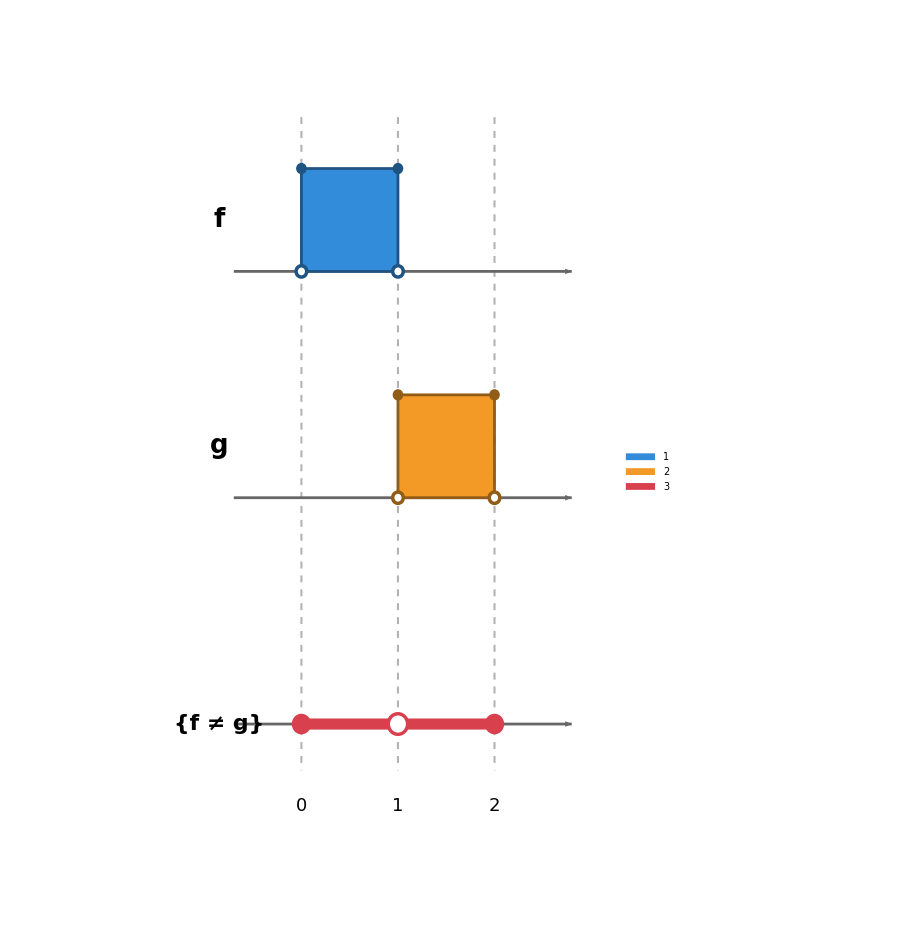

```mathematica
ClearAll[colF, colG, colD, rr, alt, y1, y2, y3, cerrado, abierto, ejeBase, indicadora, filaDif,
  guias, ticks, etiquetas, grafico8, diagrama8];

colF = RGBColor[0.2, 0.55, 0.85];
colG = RGBColor[0.95, 0.6, 0.15];
colD = RGBColor[0.85, 0.25, 0.3];
rr = 0.055;
alt = 1;
y1 = 4.4; y2 = 2.2; y3 = 0;     (* filas: f, g y el conjunto donde difieren *)

cerrado[p_, col_, r_ : rr] := {col, Disk[p, r]};
abierto[p_, col_, r_ : rr] := {White, Disk[p, r], col, AbsoluteThickness[2.5], Circle[p, r]};

ejeBase[y_] := {GrayLevel[0.4], AbsoluteThickness[2], Arrowheads[0.02],
   Arrow[{{-0.7, y}, {2.8, y}}]};

(* indicadora de [a,b]: vale 1 sobre [a,b] y 0 fuera; el área bajo ella es su integral *)
indicadora[y_, a_, b_, col_] := {
   {col, EdgeForm[{Darker[col, 0.4], AbsoluteThickness[2]}], Rectangle[{a, y}, {b, y + alt}]},
   cerrado[{a, y + alt}, Darker[col, 0.4]], cerrado[{b, y + alt}, Darker[col, 0.4]],
   abierto[{a, y}, Darker[col, 0.4]], abierto[{b, y}, Darker[col, 0.4]]};

(* f ≠ g exactamente en [0,1) y (1,2]: en 0 y en 2 solo una de las dos vale 1; en 1 coinciden *)
filaDif = {colD, AbsoluteThickness[8], CapForm["Butt"],
   Line[{{0, y3}, {1, y3}}], Line[{{1, y3}, {2, y3}}],
   cerrado[{0, y3}, colD, 0.1], abierto[{1, y3}, colD, 0.1], cerrado[{2, y3}, colD, 0.1]};

guias = {GrayLevel[0.7], Dashed, AbsoluteThickness[1.5],
   Table[Line[{{x, y1 + alt + 0.5}, {x, -0.45}}], {x, {0, 1, 2}}]};

ticks = Table[Text[Style[x, 18], {x, -0.8}], {x, {0, 1, 2}}];

etiquetas = {Black,
   Text[Style["f", 26, Bold], {-0.85, y1 + 0.5}, {1, 0}],
   Text[Style["g", 26, Bold], {-0.85, y2 + 0.5}, {1, 0}],
   Text[Style["{f ≠ g}", 22, Bold], {-0.85, y3}, {1, 0}]};

grafico8 = Graphics[{
    guias,
    ejeBase[y1], ejeBase[y2], ejeBase[y3],
    indicadora[y1, 0, 1, colF], indicadora[y2, 1, 2, colG],
    filaDif, ticks, etiquetas},
   PlotRange -> {{-2.3, 3.1}, {-1.3, 6.2}}, ImageSize -> 680];

diagrama8 = Legended[grafico8,
   SwatchLegend[{colF, colG, colD},
    {"f: integral 1", "g: integral 1", "f ≠ g: medida 2"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama8

Export[CloudObject["T3_P58_b"], diagrama8,"PNG", Background -> None,ImageResolution -> 300];
```